#### Define Functions

```mathematica
Clear["Global`*"]
(*Gamma function and its values at zero*)
γ[η_,m_,n_]:=Abs[1-(1-((η+1)/2)^2)^m]^n
γ01[m_,n_]:=γ[0,m,n]
γ02[m_,n_]:=γ[0,m,n]
NAG3one[η_,m_,n_]:=(-γ01[m,n]+(γ01[m,n]-1) η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3two[η_,m_,n_]:=(1+η-2 γ[η,m,n])/(1-2 γ01[m,n])
NAG3three[η_,m_,n_]:=(-γ01[m,n]-γ01[m,n] η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3t2one[η_,m_,n_]:=NAG3three[-η,m,n]
NAG3t2two[η_,m_,n_]:=NAG3two[-η,m,n]
NAG3t2three[η_,m_,n_]:=NAG3one[-η,m,n]
(*Shape function for AG type 1*)
NShape[η_,m_,n_]:={NAG3one[η,m,n],NAG3two[η,m,n],NAG3three[η,m,n]};
dNShape[η_,m_,n_]:=D[NShape[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(*Shape function for AG type 2*)
NShape2[η_,m_,n_]:={NAG3t2one[η,m,n],NAG3t2two[η,m,n],NAG3t2three[η,m,n]};
dNShape2[η_,m_,n_]:=D[NShape2[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(***************************************************************)
(*Function to get the M matrices: relate Nodal force and Nodal traction*)
elementMmatrix[xpos_,AGtype_]:= Module[{},
{m,n,type}={AGtype[[1]],AGtype[[2]],AGtype[[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
(*Print[AGshape[η,m,n]];*)
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
M=Table[NIntegrate[AGshape[η,m,n][[j]]*AGshape[η,m,n][[i]]*jac,{η,-1,1}],{i,1,3},{j,1,3}]
];
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
GlobalMmat[xcoord_,conns_,AGtype_]:=Module[{n=Max@Flatten@conns,GlobalMat,Me,conn},
GlobalMat=ConstantArray[0.,{n,n}];
Do[
Me=elementMmatrix[xcoord[[e]],AGtype[[e]]];
(*Print[Me//MatrixForm];*)
conn=conns[[e]];
Do[
GlobalMat[[conn[[i]],conn[[j]]]]+=Me[[i,j]],{i,3},{j,3}],
{e,Length@conns}];
GlobalMat  (* <--return M assembled*)
]
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
PxinterpolatedData[Pvec_,AGtype_,xcoord_]:=Module[{},
Pxdata={};
(*total=0;*)
Pelem=Partition[Pvec,3,2];
nelem= Length[conns];
Do[
elem=e;
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};
If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
Clear[x,η];
xη=AGshape[η,1,1].xcoord[[elem]];
ηmap=η/.NSolve[xη==x,η]//First;
ηbranches=η/. Solve[xη==x,η];
x0=xcoord[[elem]][[1]]+0.01;
vals0=N[ηbranches/. x->x0];
(* ->something like {-1.4...,-0.6...}*)
(*pick the correct branch by "in parent domain" criterion*)
ηmap=First@Pick[ηbranches,(-1<=#<=1)&/@vals0];

PinterpolatePhysical=Sum[AGshape[η,m,n][[i]]*Pelem[[elem]][[i]],{i,1,3}]/.{η->ηmap};(*geometric mapping*)
(*resultant=NIntegrate[PinterpolatePhysical,{x,xmin,xmax}];
PxResultant=total+resultant;*)

{xmin,xmax}={Min[xcoord[[elem]]],Max[xcoord[[elem]]]};
n=30;
dx=(xmax-xmin)/n;
xdata=Table[xmin+i dx,{i,0,n}];
pdata=PinterpolatePhysical/.x->xdata;
plotdata=Transpose[{xdata, pdata}];
Pxdata=AppendTo[Pxdata, plotdata];
,{e,1,nelem}];
(*Print[PxResultant];*)
Flatten[Pxdata,1]
]


ComputeResultant[Pelem_,xcoord_,AGtype_]:=Module[{},
totalResutant=0;
Do[
elem=e;
xpos=xcoord[[elem]];
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];

resultant=Pelem[[elem]].NIntegrate[AGshape[η,m,n]*jac,{η,-1,1}];
(*Print[resultant];*)
totalResutant=totalResutant+resultant;
,{e,1,Length[conns]}];
totalResutant
]
```

#### debug

```mathematica
elem=1;
xcoord={{4.,4.0625,4.25}};
Pelem={{"-2.027"×10^("8"),"-7.926"×10^("7"),"-1.810"×10^("7")}};
{m,n,type}={1,1,1};
If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
Clear[x,η];
xη=AGshape[η,1,1].xcoord[[elem]];

ηmap[x_]:=First@Select[η/. NSolve[xη==x,η],-1<=#<=1&]

(*P(η) interpolation on parent*)
Pη[η_]:=Sum[AGshape[η,m,n][[i]]*Pelem[[elem,i]],{i,1,3}];

(*----build arrays for plotting----*)
xList=Subdivide[Min@xcoord[[elem]],Max@xcoord[[elem]],10]
              (*choose your resolution*)
ηList=ηmap/@xList
```

{4.,4.025,4.05,4.075,4.1,4.125,4.15,4.175,4.2,4.225,4.25}

{-1.,-0.367544,-0.105573,0.0954451,0.264911,0.414214,0.549193,0.67332,0.788854,0.897367,1.}

```mathematica
(*test point*)
ηbranches=η/. Solve[xη==x,η];
x0=4.01;
vals0=N[ηbranches/. x->x0];
(* ->something like {-1.4...,-0.6...}*)

(*pick the correct branch by "in parent domain" criterion*)
ηgood=First@Pick[ηbranches,(-1<=#<=1)&/@vals0]
```

0.5 (-2.+√(-256.+64. x))

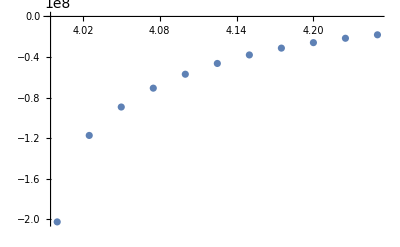

```mathematica
PinterpolatePhysical=Pη/@ηList;
plotdata=Transpose[{xList, PinterpolatePhysical}];
ListPlot[plotdata]
```

```mathematica
PinterpolatePhysical=Sum[AGshape[η,m,n][[i]]*Pelem[[elem]][[i]],{i,1,3}]/.{η->ηmap};(*geometric mapping*)
(*resultant=NIntegrate[PinterpolatePhysical,{x,xmin,xmax}];
PxResultant=total+resultant;*)

{xmin,xmax}={Min[xcoord[[elem]]],Max[xcoord[[elem]]]};
n=10;
dx=(xmax-xmin)/n;
xdata=Table[xmin+i dx,{i,0,n}];
pdata=PinterpolatePhysical/.x->xdata;
plotdata=Transpose[{xdata, pdata}];
(*Pxdata=AppendTo[Pxdata, plotdata];*)
ListLinePlot[plotdata]
```

Transpose::nmtx: The first two levels of {{4.,4.025,4.05,4.075,4.1,4.125,4.15,4.175,4.2,4.225,«1»},-1.58516×10^8 (1+ηmap-1/2 Abs[Plus[«2»]]^2)-4.05367×10^8 (-1/4-(3 ηmap)/4+1/4 Abs[Plus[«2»]]^2)-3.6203×10^7 (-1/4-ηmap/4+1/4 Abs[Plus[«2»]]^2)} cannot be transposed.

Transpose::nmtx: The first two levels of {{4.,4.025,4.05,4.075,4.1,4.125,4.15,4.175,4.2,4.225,«1»},-1.58516×10^8 (1.+ηmap-0.5 Abs[Plus[«2»]]^2)-4.05367×10^8 (-0.25-0.75 ηmap+0.25 Abs[Plus[«2»]]^2)-3.6203×10^7 (-0.25-0.25 ηmap+0.25 Abs[Plus[«2»]]^2)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{{4.,4.025,4.05,4.075,4.1,4.125,4.15,4.175,4.2,4.225,«1»},-1.58516×10^8 (1.+ηmap-0.5 Power[«2»])-4.05367×10^8 (-0.25-0.75 ηmap+0.25 Power[«2»])-3.6203×10^7 (-0.25-0.25 ηmap+0.25 Power[«2»])}] is not a list of numbers or pairs of numbers.

ListLinePlot[Transpose[{{4.,4.025,4.05,4.075,4.1,4.125,4.15,4.175,4.2,4.225,4.25},-1.58516×10^8 (1+ηmap-1/2 Abs[1+ηmap]^2)-4.05367×10^8 (-1/4-(3 ηmap)/4+1/4 Abs[1+ηmap]^2)-3.6203×10^7 (-1/4-ηmap/4+1/4 Abs[1+ηmap]^2)}]]

### P(x) comparison, QPE vs Quadratic vs AG

#### p(x) QPE: welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x) (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

-Graphics-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in η near {η} = {-0.531281}. NIntegrate obtained 4.33681×10^-19 and 2.86393×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in η near {η} = {-0.531281}. NIntegrate obtained 4.33681×10^-19 and 2.86393×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in η near {η} = {0.99944115765036580065379390180879681793157942593097686767578125}. NIntegrate obtained 4.87891×10^-19 and 2.9549×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in η near {η} = {-0.99999230143142520007055085336233890558332859654910862445831298828}. NIntegrate obtained -1.89735×10^-18 and 1.2124×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in η near {η} = {0.99999230143142520007055085336233890558332859654910862445831298828}. NIntegrate obtained -1.46367×10^-18 and 1.21161×10^-17 for the integral and error estimates.

Nodal traction vectors P(1,1) = {-2.027×10^8,-7.926×10^7,-1.810×10^7,-2.739×10^7,-2.239×10^7,-2.259×10^7,-2.128×10^7,-2.104×10^7,-2.078×10^7,-2.104×10^7,-2.128×10^7,-2.259×10^7,-2.239×10^7,-2.739×10^7,-1.810×10^7,-7.926×10^7,-2.027×10^8}

p(x) resultant force P(1,1) = -6.36293×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\QPE_Welded_punch\disp_control(40,40)_rigid_punch_(1,1,1,1,3)_dz=-0.1\NodalTraction.xlsx

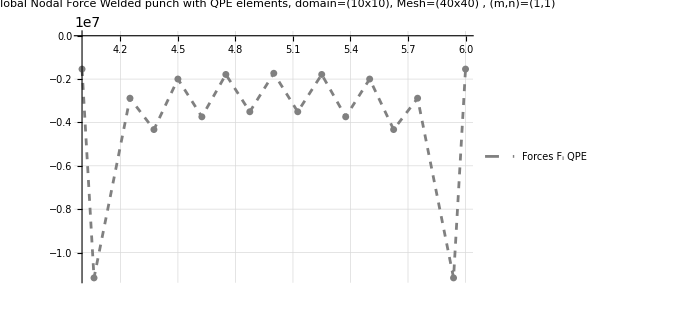

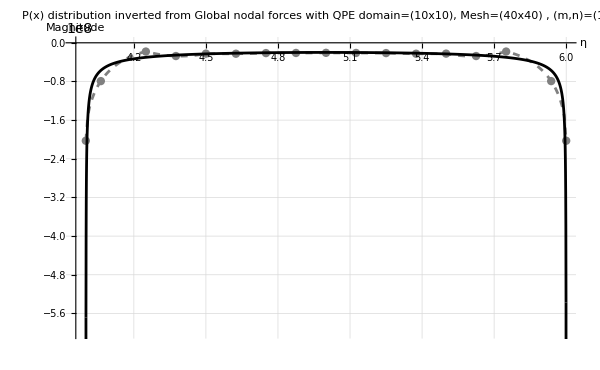

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\QPE_Welded_punch\\disp_control(40,40)_rigid_punch_(1,1,1,1,3)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*);
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch with QPE elements, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]



Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,{0, -6*10^8}},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces with QPE \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.01]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE,PxexactPlot]
```

```mathematica
Clear[nx]
```

#### p(x) Standard Quadratic: welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x) (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

Nodal traction vectors P(1,1) = {-2.075×10^8,-1.724×10^7,-5.508×10^7,-2.226×10^7,-2.784×10^7,-2.152×10^7,-2.202×10^7,-2.068×10^7,-2.090×10^7,-2.068×10^7,-2.202×10^7,-2.152×10^7,-2.784×10^7,-2.226×10^7,-5.508×10^7,-1.724×10^7,-2.075×10^8}

p(x) resultant force P(1,1) = -6.37546×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1\NodalTraction.xlsx

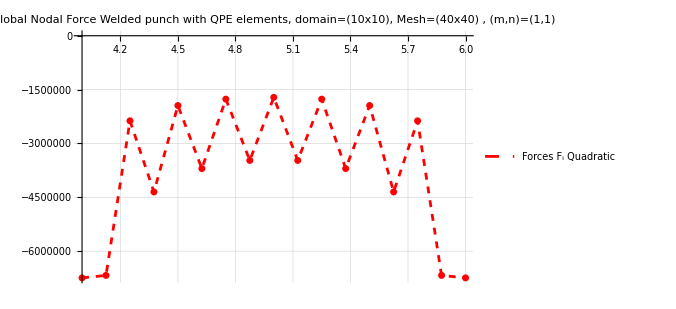

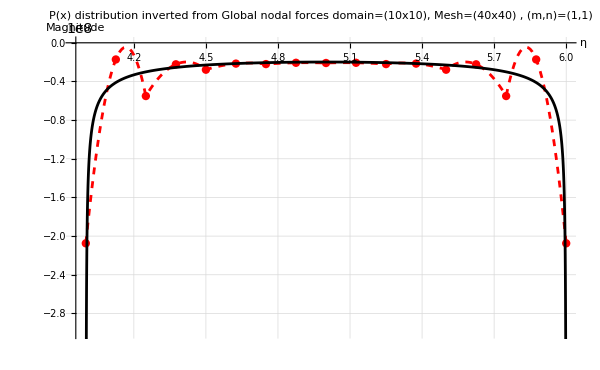

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*);
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2](*element nodal x-coordinate*);

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotQuad=ListLinePlot[Fydata,PlotStyle->{Red,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i Quadratic"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch with QPE elements, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQuad=ListPlot[Fydata,PlotStyle->{Red,PointSize[0.01]}];

Show[FvecPlotQuad,FvecDotQuad]

Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotQuad=ListLinePlot[Pxdata,PlotRange->{All,{0, -3*10^8}},PlotStyle->{Red,Dashed},PlotLegends->Placed[{"P(x) distribution Quadratic"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQuad=ListPlot[Pvecdata,PlotStyle->{Red,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQuad,PvecPlotQuad,PxexactPlot]
```

```mathematica
Clear[nx]
```

#### p(x) AG: welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x) (m1,n1,m2,n2;ngauss)(1,10,1,10;10)

{4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.125,5.25,5.375,5.5,5.625,5.75,5.875,6.}

{-3.09703×10^6,-1.33988×10^7,727507.,-4.26852×10^6,-1.96355×10^6,-3.70879×10^6,-1.77165×10^6,-3.48292×10^6,-1.72073×10^6,-3.48292×10^6,-1.77165×10^6,-3.70879×10^6,-1.96355×10^6,-4.26852×10^6,727507.,-1.33988×10^7,-3.09703×10^6}

{{1,10,1,10,2},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,10,1,10,1}}

Nodal traction vectors P(1,10) = {-4.671×10^8,-3.785×10^7,-3.166×10^7,-2.502×10^7,-2.432×10^7,-2.209×10^7,-2.148×10^7,-2.084×10^7,-2.076×10^7,-2.084×10^7,-2.148×10^7,-2.209×10^7,-2.432×10^7,-2.502×10^7,-3.166×10^7,-3.785×10^7,-4.671×10^8}

p(x) resultant force P(1,10) = -6.36482×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\NodalTraction.xlsx

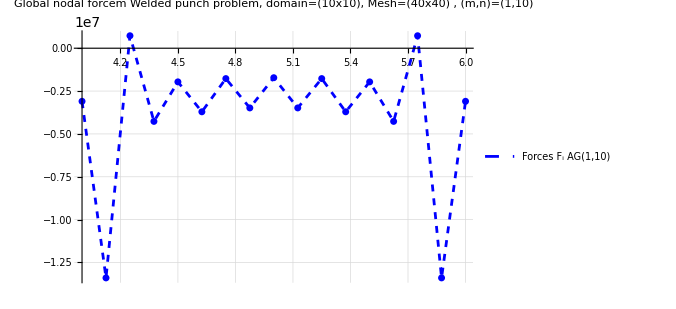

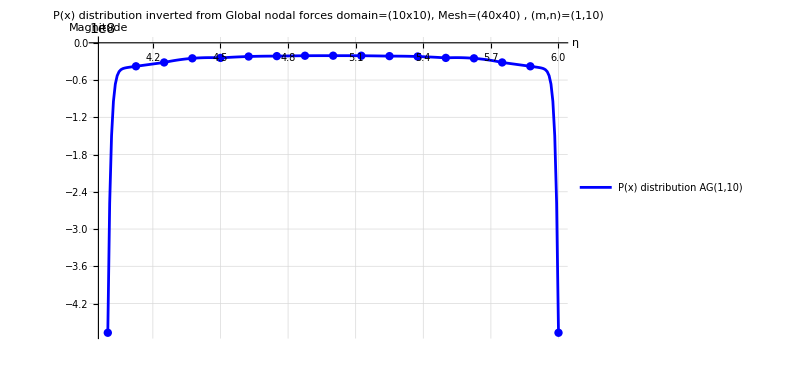

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]]
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*)
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};
AGtype

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotAG=ListLinePlot[Fydata,PlotStyle->{Blue,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i AG(1,10)"},{0.7,0.3}],PlotLabel->Style[Row[{"Global nodal forcem Welded punch problem, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotAG=ListPlot[Fydata,PlotStyle->{Blue,PointSize[0.01]}];

Show[FvecPlotAG,FvecDotAG]


Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotAG=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Blue},PlotLegends->Placed[{"P(x) distribution AG(1,10)"},{0.7,0.3}],AxesLabel->{Style["η",Bold,16],Style["Magnitude",Bold,16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], 
TicksStyle->{16,Bold}, TicksStyle->Directive["Label",Bold, 12],
GridLines->Automatic,ImageSize->600];

PvecPlotAG=ListPlot[Pvecdata,PlotStyle->{Blue,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];
Show[PxplotAG,PvecPlotAG]
```

#### Plot together

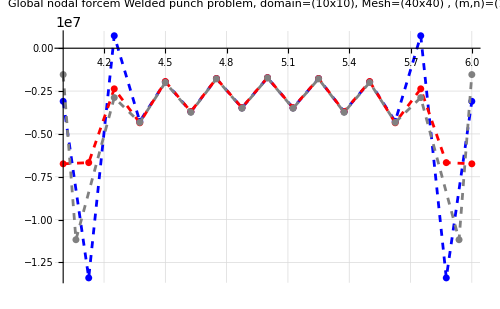

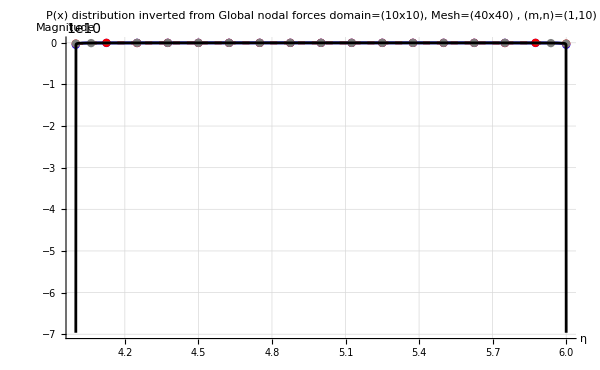

```mathematica
Show[FvecPlotAG,FvecDotAG,FvecPlotQuad,FvecDotQuad,FvecPlotQPE,FvecDotQPE]
Show[PxplotAG,PvecPlotAG,PxplotQuad,PvecPlotQuad,PxplotQPE,PvecPlotQPE,PxexactPlot,PlotRange->{{4,6},{0,-2*10^8}}]
```

```mathematica
Clear[nx]
```

```mathematica
Show[PxplotAG,PvecPlotAG,PxplotQuad,PvecPlotQuad,PxplotQPE,PvecPlotQPE,PxexactPlot,PlotRange->{{4,6},{0,-0.7*10^8}}]
```

-Graphics-

### P(x) comparison (1,1) FE inverted by AG(1,1) vs AG(1,10)

#### p(x) Standard Quadratic: welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x) (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

Nodal traction vectors P(1,1) = {-2.075×10^8,-1.724×10^7,-5.508×10^7,-2.226×10^7,-2.784×10^7,-2.152×10^7,-2.202×10^7,-2.068×10^7,-2.090×10^7,-2.068×10^7,-2.202×10^7,-2.152×10^7,-2.784×10^7,-2.226×10^7,-5.508×10^7,-1.724×10^7,-2.075×10^8}

p(x) resultant force P(1,1) = -6.37546×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1\NodalTraction.xlsx

-Graphics-

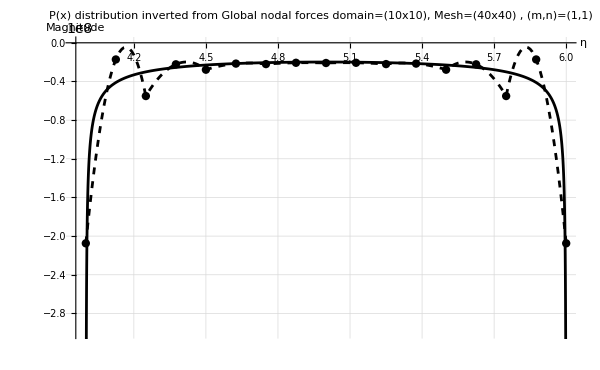

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*);
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2](*element nodal x-coordinate*);

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotQuad=ListLinePlot[Fydata,PlotStyle->{Red,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i Quadratic"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch with QPE elements, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQuad=ListPlot[Fydata,PlotStyle->{Red,PointSize[0.01]}];

Show[FvecPlotQuad,FvecDotQuad]

Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotQuad=ListLinePlot[Pxdata,PlotRange->{All,{0, -3*10^8}},PlotStyle->{Black,Dashed},PlotLegends->Placed[{"P(x) (1,1)FE inverted by AG(1,1)"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQuad=ListPlot[Pvecdata,PlotStyle->{Black,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQuad,PvecPlotQuad,PxexactPlot]
```

```mathematica
Clear[nx]
```

#### p(x) Standard Quadratic but inverted by AG (1,10): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x) (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

Nodal traction vectors P(1,10) = {-1.176×10^9,7.193×10^6,-7.409×10^7,-1.948×10^7,-3.111×10^7,-2.104×10^7,-2.260×10^7,-2.058×10^7,-2.109×10^7,-2.058×10^7,-2.260×10^7,-2.104×10^7,-3.111×10^7,-1.948×10^7,-7.409×10^7,7.193×10^6,-1.176×10^9}

p(x) resultant force P(1,10) = -6.37546×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1\NodalTraction.xlsx

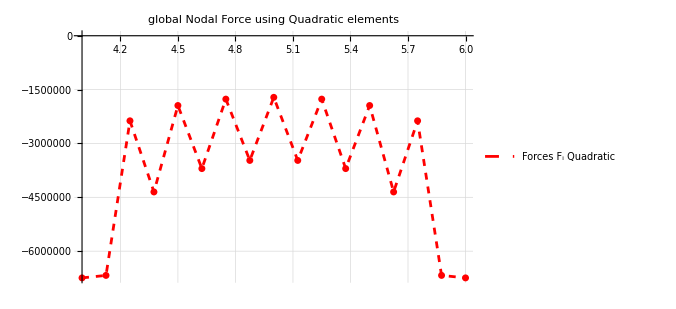

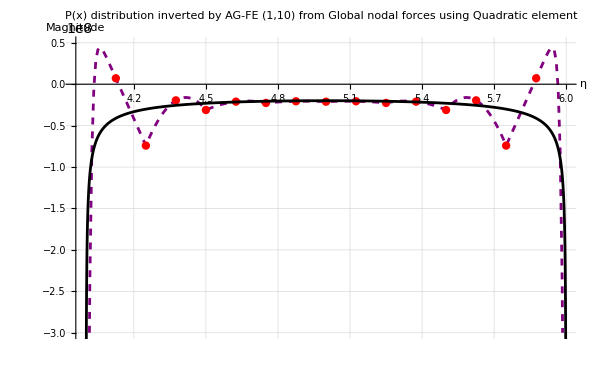

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*);
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2](*element nodal x-coordinate*);

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotQuad=ListLinePlot[Fydata,PlotStyle->{Red,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i Quadratic"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force using Quadratic elements "(*\n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")*)}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQuad=ListPlot[Fydata,PlotStyle->{Red,PointSize[0.01]}];

Show[FvecPlotQuad,FvecDotQuad]

Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotQuadAG=ListLinePlot[Pxdata,PlotRange->{All,{-3*10^8, 5*10^7}},PlotStyle->{Purple,Dashed},PlotLegends->Placed[{"P(x) (1,1)FE inverted by AG(1,10)"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted by AG-FE (1,10) from \n Global nodal forces using Quadratic element"  (*\n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")*)}],Bold, 16], GridLines->Automatic,ImageSize->600];

PvecPlotQuadAG=ListPlot[Pvecdata,PlotStyle->{Red,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQuadAG,PvecPlotQuadAG,PxexactPlot]
```

```mathematica
Clear[nx]
```

#### p(x) Standard Quadratic but inverted by AG (1,5): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x) (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

Nodal traction vectors P(1,5) = {-6.267×10^8,1.139×10^7,-7.024×10^7,-2.004×10^7,-3.045×10^7,-2.113×10^7,-2.248×10^7,-2.060×10^7,-2.105×10^7,-2.060×10^7,-2.248×10^7,-2.113×10^7,-3.045×10^7,-2.004×10^7,-7.024×10^7,1.139×10^7,-6.267×10^8}

p(x) resultant force P(1,5) = -6.37546×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1\NodalTraction.xlsx

-Graphics-

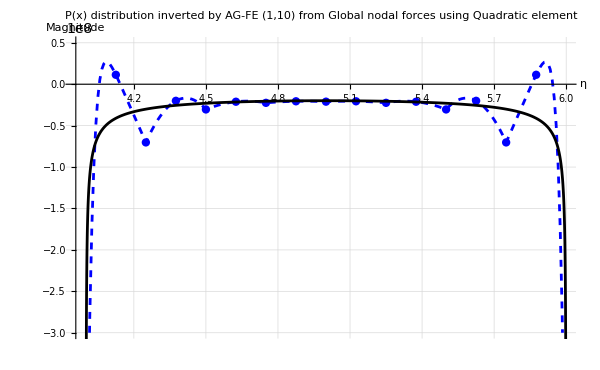

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*);
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,5,1,5};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2](*element nodal x-coordinate*);

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotQuad=ListLinePlot[Fydata,PlotStyle->{Red,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i Quadratic"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force using Quadratic elements "(*\n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")*)}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQuad=ListPlot[Fydata,PlotStyle->{Red,PointSize[0.01]}];

Show[FvecPlotQuad,FvecDotQuad]

Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

Color=Blue;
PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotQuadAG15=ListLinePlot[Pxdata,PlotRange->{All,{-3*10^8, 5*10^7}},PlotStyle->{Color,Dashed},PlotLegends->Placed[{"P(x) (1,1)FE inverted by AG(1,5)"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted by AG-FE (1,10) from \n Global nodal forces using Quadratic element"  (*\n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")*)}],Bold, 16], GridLines->Automatic,ImageSize->600];

PvecPlotQuadAG15=ListPlot[Pvecdata,PlotStyle->{Color,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQuadAG15,PvecPlotQuadAG15,PxexactPlot]
```

```mathematica
Clear[nx]
```

#### p(x) AG (1,10) but inverted by AG (1,5): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x) (m1,n1,m2,n2;ngauss)(1,10,1,10;10)

{4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.125,5.25,5.375,5.5,5.625,5.75,5.875,6.}

{-3.09703×10^6,-1.33988×10^7,727507.,-4.26852×10^6,-1.96355×10^6,-3.70879×10^6,-1.77165×10^6,-3.48292×10^6,-1.72073×10^6,-3.48292×10^6,-1.77165×10^6,-3.70879×10^6,-1.96355×10^6,-4.26852×10^6,727507.,-1.33988×10^7,-3.09703×10^6}

{{1,5,1,5,2},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,5,1,5,1}}

Nodal traction vectors P(1,5) = {-2.004×10^8,-4.833×10^7,-1.946×10^7,-2.680×10^7,-2.222×10^7,-2.240×10^7,-2.111×10^7,-2.090×10^7,-2.064×10^7,-2.090×10^7,-2.111×10^7,-2.240×10^7,-2.222×10^7,-2.680×10^7,-1.946×10^7,-4.833×10^7,-2.004×10^8}

p(x) resultant force P(1,5) = -6.36482×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\NodalTraction.xlsx

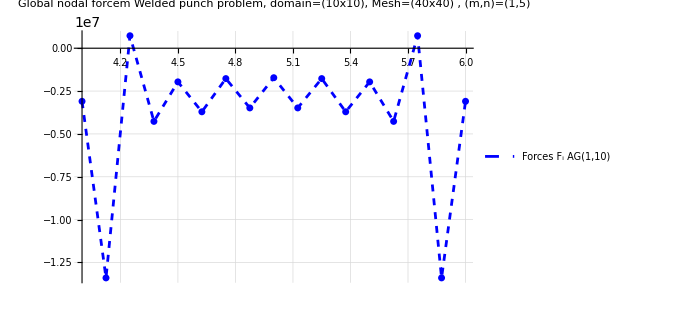

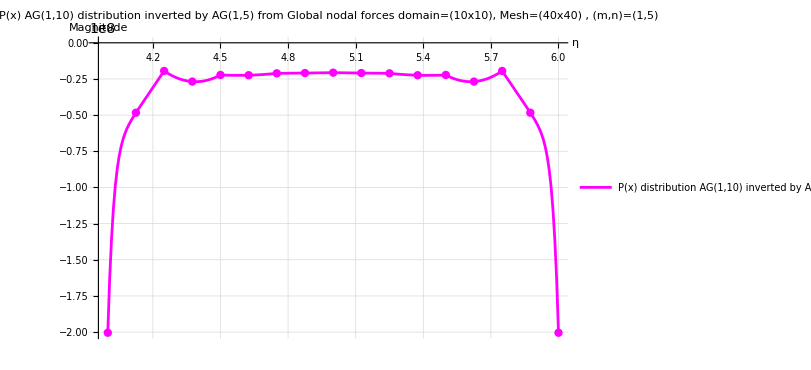

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]]
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*)
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,5,1,5};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};
AGtype

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotAG=ListLinePlot[Fydata,PlotStyle->{Blue,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i AG(1,10)"},{0.7,0.3}],PlotLabel->Style[Row[{"Global nodal forcem Welded punch problem, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotAG=ListPlot[Fydata,PlotStyle->{Blue,PointSize[0.01]}];

Show[FvecPlotAG,FvecDotAG]


Clear[x]
Color=Magenta;
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotAG11015=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Color},PlotLegends->Placed[{"P(x) distribution AG(1,10) inverted by AG(1,5)"},{0.7,0.3}],AxesLabel->{Style["η",Bold,16],Style["Magnitude",Bold,16]},PlotLabel->Style[Row[{" P(x) AG(1,10) distribution inverted by AG(1,5) from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], 
TicksStyle->{16,Bold}, TicksStyle->Directive["Label",Bold, 12],
GridLines->Automatic,ImageSize->600];

PvecPlotAG11015=ListPlot[Pvecdata,PlotStyle->{Color,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];
Show[PxplotAG11015,PvecPlotAG11015]
```

#### Altogether

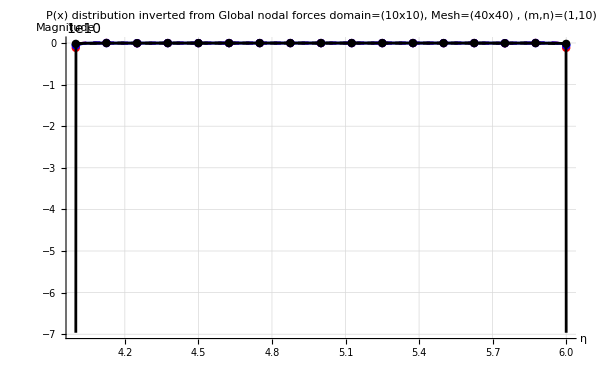

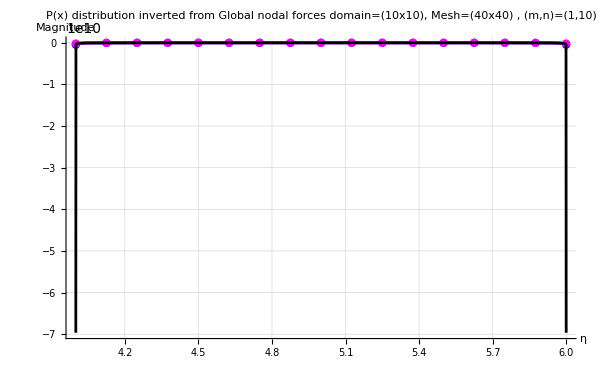

```mathematica
Show[FvecPlotQuad,FvecDotQuad,FvecPlotQPE,FvecDotQPE];
Show[PxplotAG,PvecPlotAG,PxplotQuadAG,PvecPlotQuadAG,PxplotQuadAG15,PvecPlotQuadAG15,PxplotQuad,PvecPlotQuad,PxexactPlot,PlotRange->{{4,6},{0.5*10^8,-2*10^8}}]

Show[PxplotAG,PvecPlotAG,PxplotAG11015,PvecPlotAG11015,PxexactPlot,PlotRange->{{4,6},{0.5*10^8,-2*10^8}}]
```

### P(x) comparison (1,5) FE inverted by AG(1,1) vs AG(1,10)

#### p(x) AG (1,10) inverted by AG (1,10): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]]
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*)
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};
AGtype

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Clear[x]
Color=Black;
label="P(x) distribution AG(1,10) inverted by AG(1,10)";

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotAG=ListLinePlot[Fydata,PlotStyle->{Color,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i AG(1,10)"},{0.7,0.3}],PlotLabel->Style[Row[{"Global nodal forcem Welded punch problem, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotAG=ListPlot[Fydata,PlotStyle->{Color,PointSize[0.01]}];

Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,Dashed},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotAG110110=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Color},PlotLegends->Placed[{label},{0.7,0.3}],AxesLabel->{Style["η",Bold,16],Style["Magnitude",Bold,16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], 
TicksStyle->{16,Bold}, TicksStyle->Directive["Label",Bold, 12],
GridLines->Automatic,ImageSize->600];

PvecPlotAG=ListPlot[Pvecdata,PlotStyle->{Color,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Fy110=Show[FvecPlotAG,FvecDotAG]
plot110110=Show[PxplotAG110110,PvecPlotAG]
```

{4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.125,5.25,5.375,5.5,5.625,5.75,5.875,6.}

{-3.09703×10^6,-1.33988×10^7,727507.,-4.26852×10^6,-1.96355×10^6,-3.70879×10^6,-1.77165×10^6,-3.48292×10^6,-1.72073×10^6,-3.48292×10^6,-1.77165×10^6,-3.70879×10^6,-1.96355×10^6,-4.26852×10^6,727507.,-1.33988×10^7,-3.09703×10^6}

{{1,10,1,10,2},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,10,1,10,1}}

Nodal traction vectors P(1,10) = {-4.671×10^8,-3.785×10^7,-3.166×10^7,-2.502×10^7,-2.432×10^7,-2.209×10^7,-2.148×10^7,-2.084×10^7,-2.076×10^7,-2.084×10^7,-2.148×10^7,-2.209×10^7,-2.432×10^7,-2.502×10^7,-3.166×10^7,-3.785×10^7,-4.671×10^8}

p(x) resultant force P(1,10) = -6.36482×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\NodalTraction.xlsx

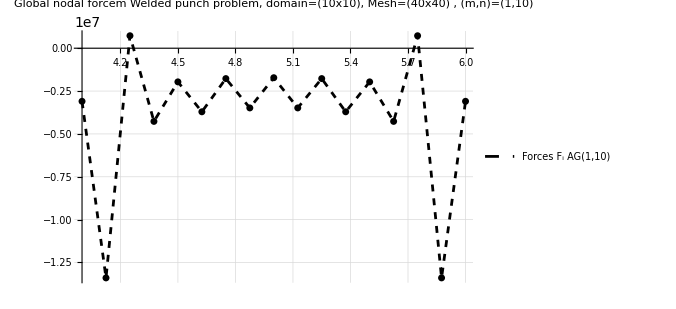

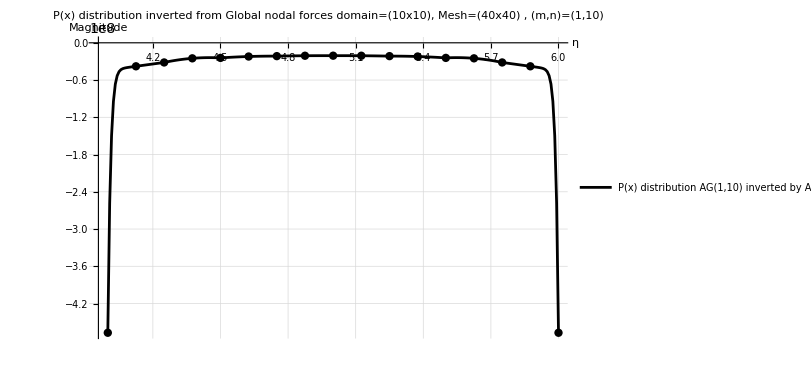

```mathematica
-6.3648218307325944*^7
```

#### p(x) AG (1,10) inverted by AG (1,8): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]]
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*)
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,8,1,8};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};
AGtype

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Clear[x]
Color=Brown;
label="P(x) distribution AG(1,10) inverted by AG(1,8)";

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotAG=ListLinePlot[Fydata,PlotStyle->{Color,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i AG(1,10)"},{0.7,0.3}],PlotLabel->Style[Row[{"Global nodal forcem Welded punch problem, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotAG=ListPlot[Fydata,PlotStyle->{Color,PointSize[0.01]}];

Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,Dashed},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotAG11018=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Color},PlotLegends->Placed[{label},{0.7,0.3}],AxesLabel->{Style["η",Bold,16],Style["Magnitude",Bold,16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], 
TicksStyle->{16,Bold}, TicksStyle->Directive["Label",Bold, 12],
GridLines->Automatic,ImageSize->600];

PvecPlotAG=ListPlot[Pvecdata,PlotStyle->{Color,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Fy110=Show[FvecPlotAG,FvecDotAG]
plot11018=Show[PxplotAG11018,PvecPlotAG]
```

{4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.125,5.25,5.375,5.5,5.625,5.75,5.875,6.}

{-3.09703×10^6,-1.33988×10^7,727507.,-4.26852×10^6,-1.96355×10^6,-3.70879×10^6,-1.77165×10^6,-3.48292×10^6,-1.72073×10^6,-3.48292×10^6,-1.77165×10^6,-3.70879×10^6,-1.96355×10^6,-4.26852×10^6,727507.,-1.33988×10^7,-3.09703×10^6}

{{1,8,1,8,2},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,8,1,8,1}}

Nodal traction vectors P(1,8) = {-3.631×10^8,-3.999×10^7,-2.879×10^7,-2.544×10^7,-2.383×10^7,-2.216×10^7,-2.139×10^7,-2.086×10^7,-2.073×10^7,-2.086×10^7,-2.139×10^7,-2.216×10^7,-2.383×10^7,-2.544×10^7,-2.879×10^7,-3.999×10^7,-3.631×10^8}

p(x) resultant force P(1,8) = -6.36482×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\NodalTraction.xlsx

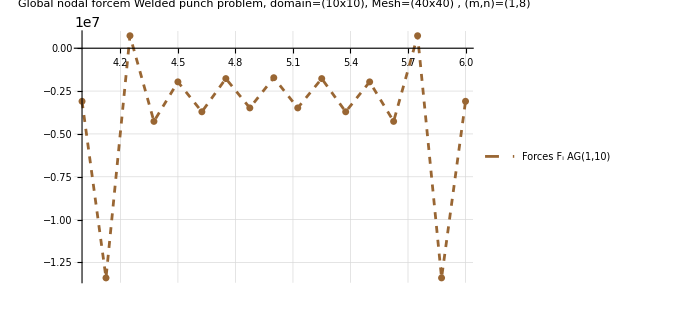

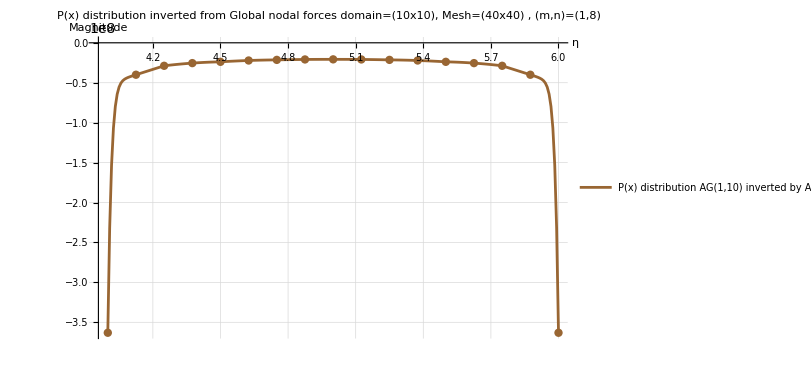

```mathematica
-6.364821830732593*^7
```

#### p(x) AG (1,5) inverted by AG (1,5): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x)

Nodal traction vectors P(1,5) = {-3.437×10^8,-2.626×10^7,-4.044×10^7,-2.442×10^7,-2.575×10^7,-2.201×10^7,-2.178×10^7,-2.087×10^7,-2.090×10^7,-2.087×10^7,-2.178×10^7,-2.201×10^7,-2.575×10^7,-2.442×10^7,-4.044×10^7,-2.626×10^7,-3.437×10^8}

p(x) resultant force P(1,5) = -6.3537×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_results\disp_control(40,40)_rigid_punch_(1,5,1,5,10)_dz=-0.1\NodalTraction.xlsx

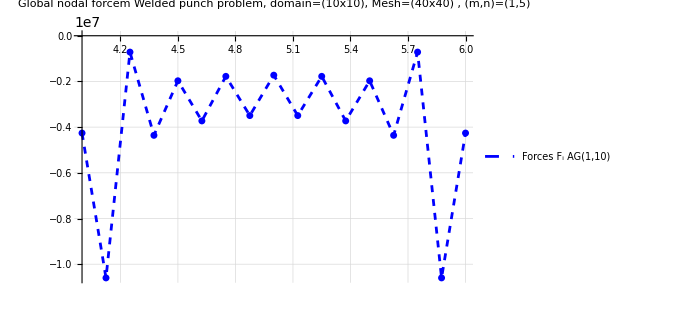

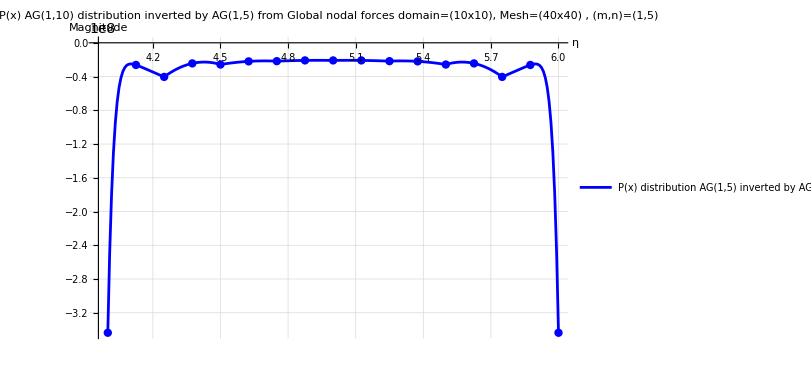

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_results\\disp_control(40,40)_rigid_punch_(1,5,1,5,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,5).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]];(*Nodal Reaction force/*)
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,5,1,5};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};
AGtype;

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotAG=ListLinePlot[Fydata,PlotStyle->{Blue,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i AG(1,10)"},{0.7,0.3}],PlotLabel->Style[Row[{"Global nodal forcem Welded punch problem, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotAG=ListPlot[Fydata,PlotStyle->{Blue,PointSize[0.01]}];

Show[FvecPlotAG,FvecDotAG]


Clear[x]
Color=Blue;
label="P(x) distribution AG(1,5) inverted by AG(1,5)";
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotAG=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Color},PlotLegends->Placed[{label},{0.7,0.3}],AxesLabel->{Style["η",Bold,16],Style["Magnitude",Bold,16]},PlotLabel->Style[Row[{" P(x) AG(1,10) distribution inverted by AG(1,5) from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], 
TicksStyle->{16,Bold}, TicksStyle->Directive["Label",Bold, 12],
GridLines->Automatic,ImageSize->600];

PvecPlotAG=ListPlot[Pvecdata,PlotStyle->{Color,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];
plot1515=Show[PxplotAG,PvecPlotAG]
```

#### p(x) AG (1,5) inverted by AG (1,10): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x)

Nodal traction vectors P(1,10) = {-6.995×10^8,-2.153×10^7,-4.908×10^7,-2.315×10^7,-2.723×10^7,-2.180×10^7,-2.204×10^7,-2.083×10^7,-2.099×10^7,-2.083×10^7,-2.204×10^7,-2.180×10^7,-2.723×10^7,-2.315×10^7,-4.908×10^7,-2.153×10^7,-6.995×10^8}

p(x) resultant force P(1,10) = -6.3537×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_results\disp_control(40,40)_rigid_punch_(1,5,1,5,10)_dz=-0.1\NodalTraction.xlsx

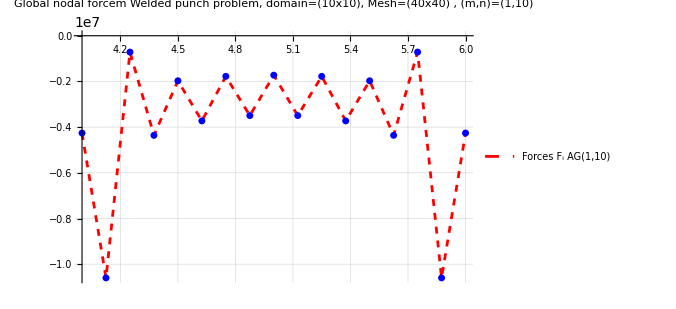

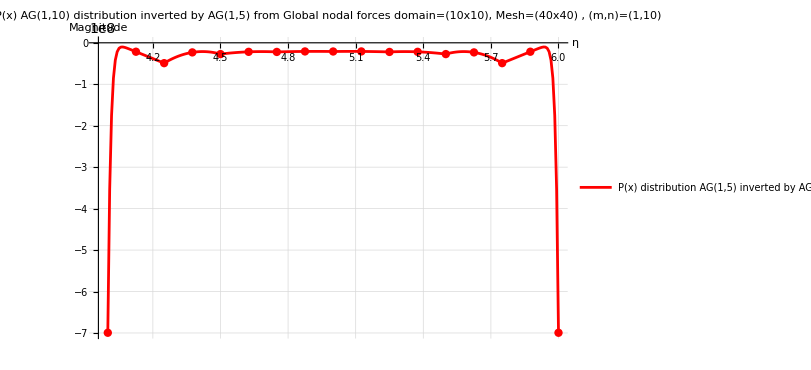

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_results\\disp_control(40,40)_rigid_punch_(1,5,1,5,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,5).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]];(*Nodal Reaction force/*)
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};
AGtype;

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]


Clear[x]
Color=Red;
label="P(x) distribution AG(1,5) inverted by AG(1,10)";

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotAG=ListLinePlot[Fydata,PlotStyle->{Color,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i AG(1,10)"},{0.7,0.3}],PlotLabel->Style[Row[{"Global nodal forcem Welded punch problem, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotAG=ListPlot[Fydata,PlotStyle->{Blue,PointSize[0.01]}];

pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotAG=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Color},PlotLegends->Placed[{label},{0.7,0.3}],AxesLabel->{Style["η",Bold,16],Style["Magnitude",Bold,16]},PlotLabel->Style[Row[{" P(x) AG(1,10) distribution inverted by AG(1,5) from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], 
TicksStyle->{16,Bold}, TicksStyle->Directive["Label",Bold, 12],
GridLines->Automatic,ImageSize->600];

PvecPlotAG=ListPlot[Pvecdata,PlotStyle->{Color,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Fy15=Show[FvecPlotAG,FvecDotAG]
plot15110=Show[PxplotAG,PvecPlotAG]
```

#### p(x) AG (1,8) inverted by AG (1,8): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x)

Nodal traction vectors P(1,8) = {-4.216×10^8,-3.454×10^7,-3.462×10^7,-2.483×10^7,-2.482×10^7,-2.208×10^7,-2.159×10^7,-2.086×10^7,-2.081×10^7,-2.086×10^7,-2.159×10^7,-2.208×10^7,-2.482×10^7,-2.483×10^7,-3.462×10^7,-3.454×10^7,-4.216×10^8}

p(x) resultant force P(1,8) = -6.35987×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_results\disp_control(40,40)_rigid_punch_(1,8,1,8,10)_dz=-0.1\NodalTraction.xlsx

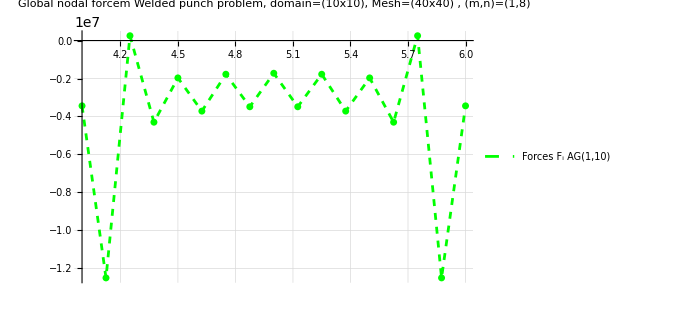

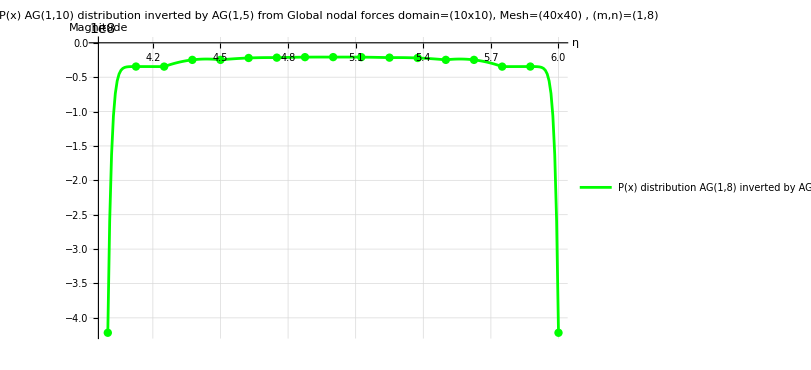

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_results\\disp_control(40,40)_rigid_punch_(1,8,1,8,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,8).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]];(*Nodal Reaction force/*)
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,8,1,8};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};
AGtype;

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]


Clear[x]
Color=Green;
label="P(x) distribution AG(1,8) inverted by AG(1,8)";


Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotAG=ListLinePlot[Fydata,PlotStyle->{Color,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i AG(1,10)"},{0.7,0.3}],PlotLabel->Style[Row[{"Global nodal forcem Welded punch problem, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotAG=ListPlot[Fydata,PlotStyle->{Color,PointSize[0.01]}];


pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotAG=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Color},PlotLegends->Placed[{label},{0.7,0.3}],AxesLabel->{Style["η",Bold,16],Style["Magnitude",Bold,16]},PlotLabel->Style[Row[{" P(x) AG(1,10) distribution inverted by AG(1,5) from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], 
TicksStyle->{16,Bold}, TicksStyle->Directive["Label",Bold, 12],
GridLines->Automatic,ImageSize->600];

PvecPlotAG=ListPlot[Pvecdata,PlotStyle->{Color,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Fy18=Show[FvecPlotAG,FvecDotAG]
plot1818=Show[PxplotAG,PvecPlotAG]
```

#### p(x) AG (1,8) inverted by AG (1,10): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x)

Nodal traction vectors P(1,10) = {-5.363×10^8,-3.283×10^7,-3.721×10^7,-2.445×10^7,-2.526×10^7,-2.201×10^7,-2.166×10^7,-2.085×10^7,-2.084×10^7,-2.085×10^7,-2.166×10^7,-2.201×10^7,-2.526×10^7,-2.445×10^7,-3.721×10^7,-3.283×10^7,-5.363×10^8}

p(x) resultant force P(1,10) = -6.35987×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_results\disp_control(40,40)_rigid_punch_(1,8,1,8,10)_dz=-0.1\NodalTraction.xlsx

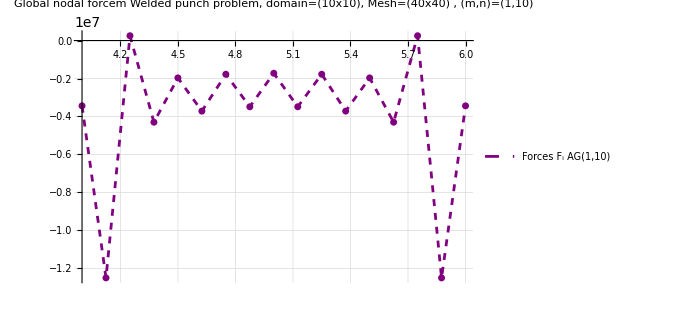

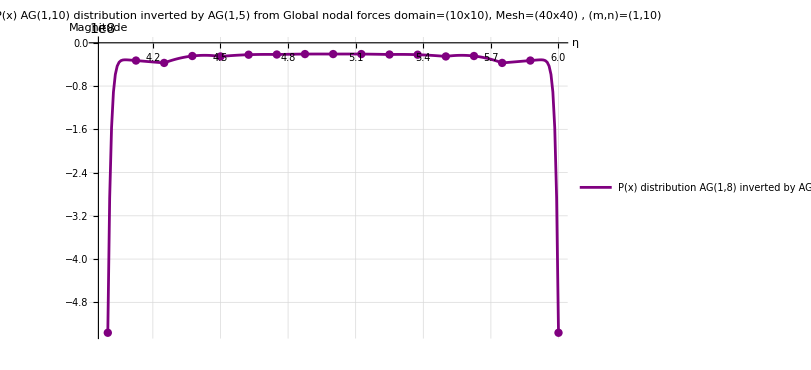

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_results\\disp_control(40,40)_rigid_punch_(1,8,1,8,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,8).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]];(*Nodal Reaction force/*)
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};
AGtype;

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]


Clear[x]
Color=Purple;
label="P(x) distribution AG(1,8) inverted by AG(1,10)";


Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotAG=ListLinePlot[Fydata,PlotStyle->{Color,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i AG(1,10)"},{0.7,0.3}],PlotLabel->Style[Row[{"Global nodal forcem Welded punch problem, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotAG=ListPlot[Fydata,PlotStyle->{Color,PointSize[0.01]}];


pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotAG=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Color},PlotLegends->Placed[{label},{0.7,0.3}],AxesLabel->{Style["η",Bold,16],Style["Magnitude",Bold,16]},PlotLabel->Style[Row[{" P(x) AG(1,10) distribution inverted by AG(1,5) from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], 
TicksStyle->{16,Bold}, TicksStyle->Directive["Label",Bold, 12],
GridLines->Automatic,ImageSize->600];

PvecPlotAG=ListPlot[Pvecdata,PlotStyle->{Color,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Fy18=Show[FvecPlotAG,FvecDotAG]
plot18110=Show[PxplotAG,PvecPlotAG]
```

#### Altogether

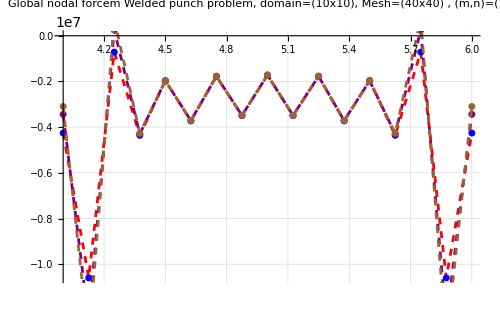

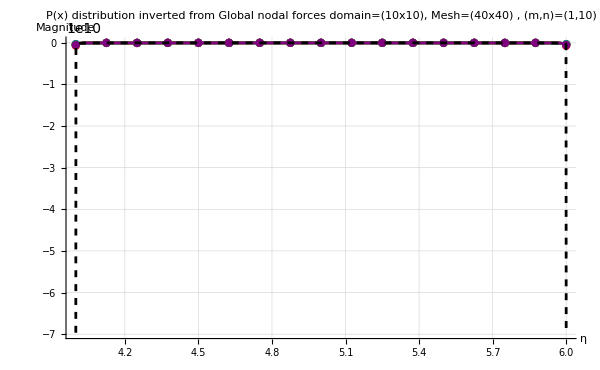

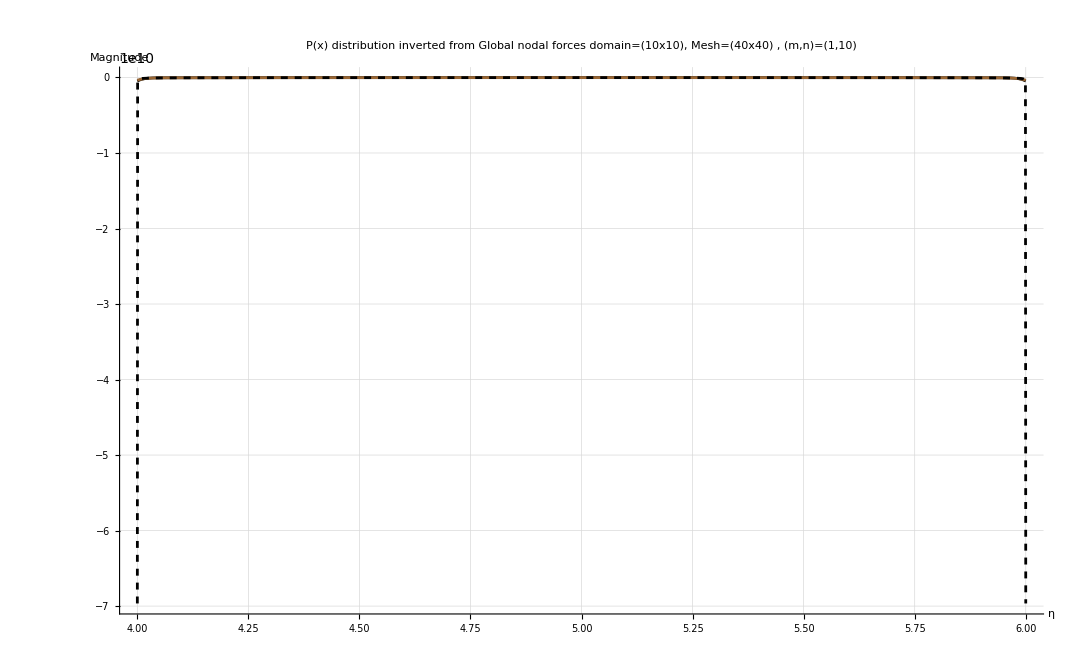

```mathematica
Show[Fy15,Fy18,Fy110]
Show[plot110110,plot11018,plot1515,plot15110,plot1818,plot18110,PxexactPlot,PlotRange->{{4,6},{0.5*10^8,-2*10^8}}]
Show[PxplotAG110110,PxplotAG11018,PxexactPlot,PlotRange->{{4,6},{0.5*10^8,-2*10^8}}]
```

### Q(x)

#### q(x): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x) (m1,n1,m2,n2;ngauss)(1,10,1,10;10)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,6]](*Nodal Reaction force/*)
```

{-1.81599×10^6,-3.11717×10^6,620272.,-179951.,-90902.8,-114925.,-34977.5,-34318.7,-3.35276×10^-8,34318.7,34977.5,114925.,90902.8,179951.,-620272.,3.11717×10^6,1.81599×10^6}

{{4.,4.125,4.25},{4.25,4.375,4.5},{4.5,4.625,4.75},{4.75,4.875,5.},{5.,5.125,5.25},{5.25,5.375,5.5},{5.5,5.625,5.75},{5.75,5.875,6.}}

Nodal traction vectors q(x) (1,10) = {-3.022×10^8,-1.469×10^6,-8.947×10^6,77184.536,-2.468×10^6,-469395.349,-672464.631,-173332.194,-2.739×10^-7,173332.194,672464.631,469395.349,2.468×10^6,-77184.536,8.947×10^6,1.469×10^6,3.022×10^8}

q(x) resultant force Q(1,10) = -1.90642×10^-6

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\NodalTraction.xlsx

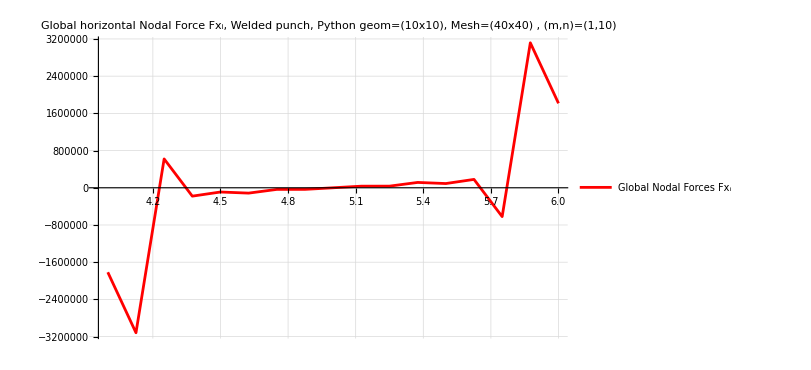

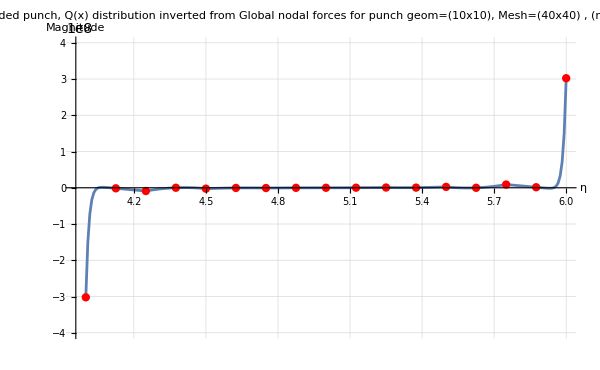

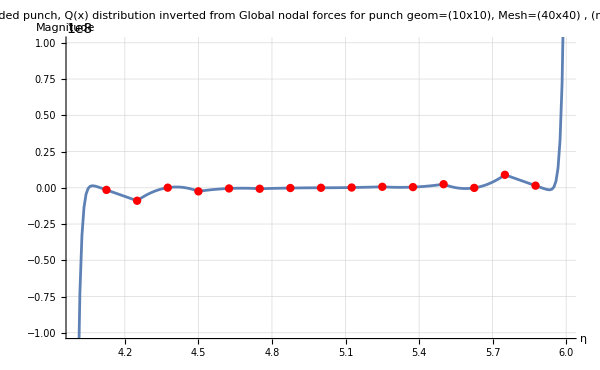

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoordglobal=Table[4+0.125i,{i,0,nele*2}];(*Global nodal 0.0625 (80x80 mesh) x-coordinate*)
xcoord=Partition[xcoordglobal,3,2](*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors q(x) (",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"q(x) resultant force Q(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlot=ListLinePlot[Fydata,PlotStyle->{Red,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"Global Nodal Forces Fx_i"},{0.8,0.3}],PlotRange->{All,{-4*10^6, 4*10^6}},PlotLabel->Style[Row[{" Global horizontal Nodal Force Fx_i, Welded punch, Python \n geom=(",gx,"x",gy,"), Mesh=(", nx,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
(*Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.8,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];*)
(**********************)
Pxplot=ListLinePlot[Pxdata,PlotRange->{All,{-4*10^8, 4*10^8}},PlotLegends->Placed[{"Q(x) distribution"},{0.8,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" Welded punch, Q(x) distribution inverted from Global nodal forces for punch \n geom=(",gx,"x",gy,"), Mesh=(",nx,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlot=ListPlot[Pvecdata,PlotStyle->{Red,PointSize[0.01]},PlotLegends->Placed[{"Nodal traction Q_i"},{0.8,0.3}]];

Show[Pxplot,PvecPlot]
Show[Pxplot,PvecPlot,PlotRange->{All,{-1*10^8, 1*10^8}}]
```

#### q(x): welded punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x) (m1,n1,m2,n2;ngauss)(1,1,1,1;10)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,6]](*Nodal Reaction force/*)
```

{-3.25509×10^6,-938067.,-120792.,-278739.,-77207.1,-115976.,-32623.2,-32967.2,-2.42144×10^-8,32967.2,32623.2,115976.,77207.1,278739.,120792.,938067.,3.25509×10^6}

Nodal traction vectors q(x) (1,1) = {-1.063×10^8,8.485×10^6,-1.782×10^7,580327.766,-3.551×10^6,-323928.761,-815947.793,-145260.389,-1.365×10^-7,145260.389,815947.793,323928.761,3.551×10^6,-580327.766,1.782×10^7,-8.485×10^6,1.063×10^8}

q(x) resultant force Q(1,1) = -2.18395×10^-6

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1\NodalTraction.xlsx

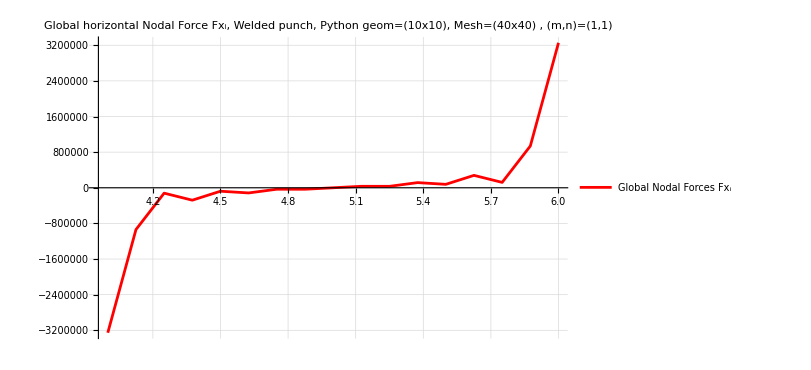

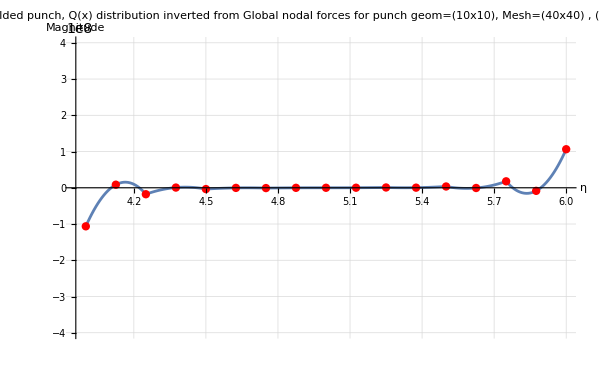

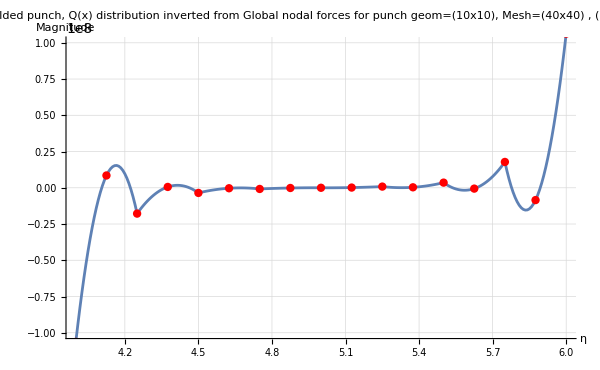

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoordglobal=Table[4+0.125i,{i,0,nele*2}];(*Global nodal 0.0625 (80x80 mesh) x-coordinate*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors q(x) (",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"q(x) resultant force Q(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlot=ListLinePlot[Fydata,PlotStyle->{Red,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"Global Nodal Forces Fx_i"},{0.8,0.3}],PlotRange->{All,{-4*10^6, 4*10^6}},PlotLabel->Style[Row[{" Global horizontal Nodal Force Fx_i, Welded punch, Python \n geom=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
(*Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.8,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];*)
(**********************)
Pxplot=ListLinePlot[Pxdata,PlotRange->{All,{-4*10^8, 4*10^8}},PlotLegends->Placed[{"Q(x) distribution"},{0.8,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" Welded punch, Q(x) distribution inverted from Global nodal forces for punch \n geom=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlot=ListPlot[Pvecdata,PlotStyle->{Red,PointSize[0.01]},PlotLegends->Placed[{"Nodal traction Q_i"},{0.8,0.3}]];

Show[Pxplot,PvecPlot]
Show[Pxplot,PvecPlot,PlotRange->{All,{-1*10^8, 1*10^8}}]
```